# Data Processing

## Part One

Setting up enviroment and importing data from .xlsx file

```mathematica
SetDirectory[NotebookDirectory[]];
dataOne = Import["Experimental Data.xlsx"][[1]];
```

Importing selected tables

```mathematica
tableOneLaser=dataOne[[4;;11,3;;4]];
tableOneRed=dataOne[[19;;23,3;;4]];
tableOneGreen=dataOne[[34;;38,3;;4]];
```

Fitting points

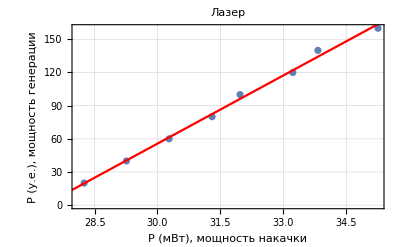

| Estimate | Standard Error | t-Statistic | P-Value
1 | -561.011 | 17.6801 | -31.7312 | 6.51047×10^-8
x | 20.5557 | 0.556877 | 36.9124 | 2.63793×10^-8

```mathematica
FitOneLaser=LinearModelFit[tableOneLaser,x,x];
laserOnePlot=Show[
ListPlot[tableOneLaser,PlotTheme->"Detailed",FrameLabel->{"P (мВт), мощность накачки", "P (у.е.), мощность генерации"},PlotLabel->"Лазер"],
Plot[FitOneLaser["BestFit"],{x,0,Max[tableOneLaser[[All,1]]]},PlotStyle->Red]
]
laserOneTable=FitOneLaser["ParameterTable"]
```

The same with other points

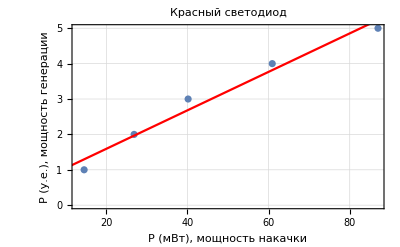

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.506827 | 0.276519 | 1.83288 | 0.164198
x | 0.0543438 | 0.00526014 | 10.3312 | 0.00193444

```mathematica
FitOneRed=LinearModelFit[tableOneRed,x,x];
redOnePlot=Show[
ListPlot[tableOneRed,PlotTheme->"Detailed",FrameLabel->{"P (мВт), мощность накачки", "P (у.е.), мощность генерации"},PlotLabel->"Красный светодиод"],
Plot[FitOneRed["BestFit"],{x,0,Max[tableOneRed[[All,1]]]},PlotStyle->Red]
]
redOneTable=FitOneRed["ParameterTable"]
```

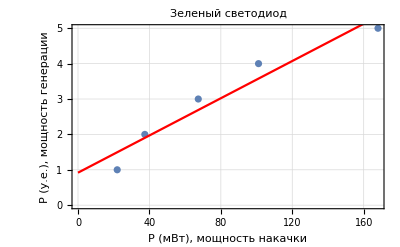

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.917949 | 0.377296 | 2.43297 | 0.0930825
x | 0.0262971 | 0.0039827 | 6.60283 | 0.00707184

```mathematica
FitOneGreen=LinearModelFit[tableOneGreen,x,x];
greenOnePlot=Show[
ListPlot[tableOneGreen,PlotTheme->"Detailed",FrameLabel->{"P (мВт), мощность накачки", "P (у.е.), мощность генерации"},PlotLabel->"Зеленый светодиод"],Plot[FitOneGreen["BestFit"],{x,0,Max[tableOneGreen[[All,1]]]},PlotStyle->Red]
]
greenOneTable=FitOneGreen["ParameterTable"]
```

Now we can export our plots

```mathematica
Export["laserOnePlot.svg",laserOnePlot,ImageSize->700];
Export["redOnePlot.svg",redOnePlot,ImageSize->700];
Export["greenOnePlot.svg",greenOnePlot,ImageSize->700];
Export["approxes.xlsx",{Normal[laserOneTable][[1]],Normal[redOneTable][[1]],Normal[greenOneTable][[1]]}];
```

## Part Two

Setting up environment and importing data from .xlsx file and outputting

```mathematica
SetDirectory[NotebookDirectory[]];
data =Import["Experimental Data.xlsx"][[1]];
```

```mathematica
tablesLaser ={
data[[8;;16,12;;13]],
data[[22;;37,12;;13]],
data[[43;;54,12;;13]]
}
```

{{{651.,3.8},{651.4,4.7},{651.6,5.9},{651.8,13.},{652.,22.7},{655.,15.2},{655.2,4.9},{655.4,4.1},{656.,3.7}},{{651.,4.23},{651.4,4.27},{651.6,4.29},{651.8,4.3},{652.,4.32},{652.2,4.33},{652.4,4.34},{652.6,4.35},{653.4,4.36},{654.,4.36},{654.2,4.34},{654.8,4.31},{655.,4.29},{655.2,4.27},{655.6,4.24},{656.,4.2}},{{651.,3.6},{651.2,4.},{651.4,5.},{651.6,6.2},{651.8,8.2},{652.,22.6},{655.,22.6},{655.2,5.4},{655.4,3.7},{655.6,3.3},{655.8,3.1},{656.,2.9}}}

Since we approximate our points with Gaussian, we have to bring the formula

```mathematica
model[x_]:=ampl*Exp[-(x-x0)^2/(2σ)];
```

Now we can start fitting.

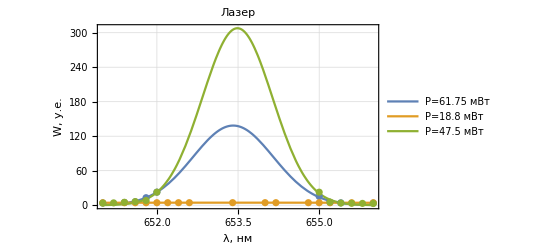

```mathematica
fits={};
laserWidths={};
plots={};
For[i=1,i≤3,i++,
AppendTo[fits,FindFit[tablesLaser[[i]],model[x],{ampl,{x0,653.5},σ},x]];
AppendTo[plots,model[x]/.fits[[i]]]]
laserPlots=Show[Plot[plots,{x,Min[tablesLaser[[1]][[All,1]]],Max[tablesLaser[[1]][[All,1]]]},PlotTheme->"Detailed",PlotLegends->{"P=61.75 мВт","P=18.8 мВт","P=47.5 мВт"},PlotLabel->"Лазер",FrameLabel->{"λ, нм","W, у.е."}],ListPlot[tablesLaser]]
laserPeaks={};
AppendTo[laserPeaks,x0/.fits];
AppendTo[laserWidths,σ/.fits];
```

The same way we get plot for Red LED

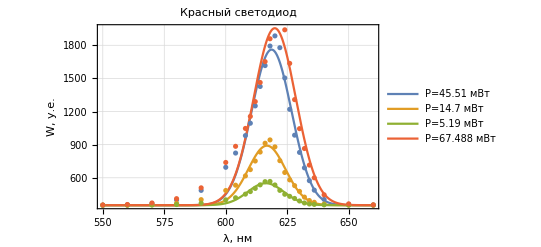

```mathematica
movingTable=Transpose[{Table[0,32-7],Table[data[[8,24]],32-7]}];
tablesRed={
data[[8;;32,23;;24]]-movingTable,
data[[39;;63,23;;24]]-movingTable,
data[[70;;94,23;;24]]-movingTable,
data[[101;;125,23;;24]]-movingTable
};
fits={};
plots={};
For[i=1,i≤4,i++,
AppendTo[fits,FindFit[tablesRed[[i]],model[x],{ampl,{x0,619},σ},x]];
AppendTo[plots,model[x]/.fits[[i]]]]
redPlots=Show[Plot[Evaluate[plots+Table[data[[8,24]],4]],{x,Min[tablesRed[[1]][[All,1]]],Max[tablesRed[[1]][[All,1]]]},PlotTheme->"Detailed",PlotLegends->{"P=45.51 мВт","P=14.7 мВт","P=5.19 мВт","P=67.488 мВт"},PlotLabel->"Красный светодиод",PlotRange->Full,FrameLabel->{"λ, нм","W, у.е."}],ListPlot[tablesRed+Table[movingTable,4]]]
redPeaks={};
redWidths={};
AppendTo[redPeaks,x0/.fits];
AppendTo[redWidths,σ/.fits];
```

Plot for Green LED

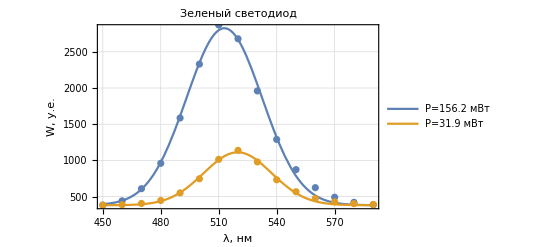

```mathematica
tablesGreen={
data[[8;;22,34;;35]]-Table[{0,data[[8,35]]-1},22-7],
data[[29;;43,34;;35]]-Table[{0,data[[29,35]]-1},22-7]
};
fits={};
plots={};
For[i=1,i≤2,i++,
AppendTo[fits,FindFit[tablesGreen[[i]],model[x],{{ampl,2650},{x0,510},{σ,25}},x]];
AppendTo[plots,model[x]/.fits[[i]]]]
greenPlots=Show[Plot[Evaluate[plots+Table[data[[8,35]]-1,2]],{x,Min[tablesGreen[[1]][[All,1]]],Max[tablesGreen[[1]][[All,1]]]},PlotTheme->"Detailed",PlotLegends->{"P=156.2 мВт","P=31.9 мВт"},PlotLabel->"Зеленый светодиод",PlotRange->Full,FrameLabel->{"λ, нм","W, у.е."}],ListPlot[tablesGreen+Table[Table[{0,data[[8,35]]-1},22-7],2]]]
greenPeaks={};
greenWidths={};
AppendTo[greenPeaks,x0/.fits];
AppendTo[greenWidths,σ/.fits];
```

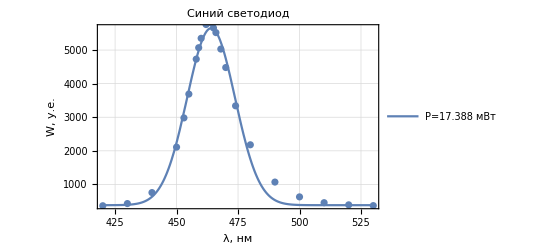

```mathematica
tablesBlue={
data[[8;;29,45;;46]]-Table[{0,data[[8,35]]-1},29-7]
};
fits={};
plots={};
For[i=1,i≤1,i++,
AppendTo[fits,FindFit[tablesBlue[[i]],model[x],{ampl,{x0,460},σ},x]];
AppendTo[plots,model[x]/.fits[[i]]]]
bluePlots=Show[Plot[Evaluate[plots+Table[{data[[8,35]]-1},1]],{x,Min[tablesBlue[[1]][[All,1]]],Max[tablesBlue[[1]][[All,1]]]},PlotTheme->"Detailed",PlotLegends->{"P=17.388 мВт"},PlotLabel->"Синий светодиод",PlotRange->Full,FrameLabel->{"λ, нм","W, у.е."}],ListPlot[tablesBlue+{Table[{0,data[[8,35]]-1},29-7]}]]
bluePeaks={};
blueWidths={};
AppendTo[bluePeaks,x0/.fits];
AppendTo[blueWidths,σ/.fits];
```

Finally we export our plots

```mathematica
Export["laser.svg",laserPlots,ImageSize->700];
Export["red.svg",redPlots,ImageSize->700];
Export["green.svg",greenPlots,ImageSize->700];
Export["blue.svg",bluePlots,ImageSize->700];
```

And generate table with peak values

```mathematica
powers={};
Export["peaks.xlsx",{
{"P, мВт",61.75,18.8,47.5},
Insert[laserPeaks,"Лазер, пик",{1,1}][[1]],
Insert[√laserWidths*√(2Log[2]),"Лазер, разброс", {1,1}][[1]],
{"P, мВт",45.51,14.7,5.19,67.488},
Insert[redPeaks,"Красный, пик",{1,1}][[1]],
Insert[√redWidths*√(2Log[2]),"Красный, разброс", {1,1}][[1]],
{"P, мВт",156.2,31.9},
Insert[greenPeaks,"Зеленый, пик",{1,1}][[1]],
Insert[√greenWidths*√(2Log[2]),"Зеленый, разброс", {1,1}][[1]],
{"P, мВт",17.388},
Insert[bluePeaks,"Синий, пик",{1,1}][[1]],
Insert[√blueWidths*√(2Log[2]),"Синий, разброс", {1,1}][[1]]
}];
```